```mathematica
X1dot = 1/10*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2dot = X1+1/10*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;
flow = {X1dot, X2dot}

dynsys = {X1'[t]== 1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t] == X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
sol[T_]:=NDSolve[Join[dynsys,Thread[{X1[0],X2[0]}== {1/Sqrt[10], 0}]],{X1[t],X2[t]},{t,0,T}];
```

{X1/10-X1^3-X2-X1^2 X2-X1 X2^2-X2^3,X1+X1^3+X2/10-X1^2 X2+X1 X2^2-X2^3}

X1/10-X1^3-X2-X1^2 X2-X1 X2^2-X2^3

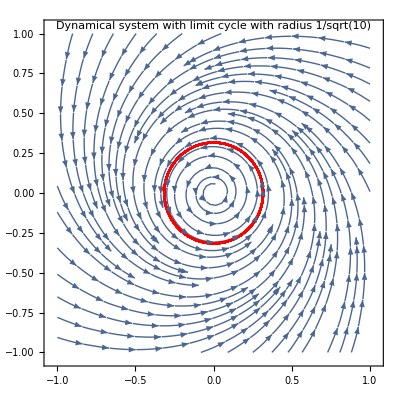

```mathematica
Tmax = 100;
text = Graphics[Text["Dynamical system with limit cycle with radius 1/sqrt(10)", {0,1.05}]];
text2 = Graphics[Text["Saddle node", {0.7, 0.4}]];
text3 = Graphics[Text["Unstable spiral", {0.05,0.2}]];
text4 = Graphics[Text["Homoclinic orbit", {0.05, 0.4}]];
p0 =Show[StreamPlot[flow,{X1,-1,1},{X2,-1,1}],ParametricPlot[Evaluate[{X1[t],X2[t]}/.sol[Tmax]],{t,0,Tmax},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}}], text];
img =(p0//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05, 0.05}],Arrow[x]}
```

```mathematica
timeflow= {1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
```

```mathematica
stabmat = D[timeflow,{{X1[t],X2[t]}}]
```

{{1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2,-1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2},{1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2,1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2}}

```mathematica
stabmat//MatrixForm
stabmat[[1]][[1]]
```

(1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2 | -1-X1[t]^2-2 X1[t] X2[t]-3 X2[t]^2
1+3 X1[t]^2-2 X1[t] X2[t]+X2[t]^2 | 1/10-X1[t]^2+2 X1[t] X2[t]-3 X2[t]^2)

1/10-3 X1[t]^2-2 X1[t] X2[t]-X2[t]^2

```mathematica
dsol= NDSolve[Join[{X1'[t]== 1/10*X1[t]-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,X2'[t] == X1[t]+1/10*X2[t]+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t], M11'[t] == stabmat[[1]][[1]]*M11[t]+stabmat[[1]][[2]]*M21[t], M12'[t] == stabmat[[1]][[1]]*M12[t]+stabmat[[1]][[2]]*M22[t], M21'[t] == stabmat[[2]][[1]]*M11[t]+stabmat[[2]][[2]]*M21[t], M22'[t]==stabmat[[2]][[1]]*M12[t]+stabmat[[2]][[2]]*M22[t],X1[0] == 1/Sqrt[10], X2[0]== 0, M11[0] == 1, M12[0]== 0, M21[0]==0,M22[0]==1}],{X1[t],X2[t], M11[t],M12[t],M21[t],M22[t]},{t,0,Tmax}];

Tmax = 2*Pi/(1+1/10);
```

Part::partd: Part specification stabmat⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NDSolve::ndnl: Endpoint Tmax in {t,0.,Tmax} is not a real number.

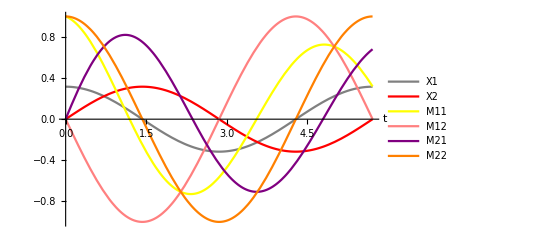

```mathematica
p1 = Plot[{X1[t]}/.dsol, {t, 0, Tmax}, PlotStyle-> Gray, PlotLegends-> {"X1"}, AxesLabel->{"t", ""}];
p2 = Plot[X2[t]/.dsol, {t, 0, Tmax}, PlotStyle->Red, PlotLegends-> {"X2"}];
p3 = Plot[M11[t]/.dsol, {t, 0, Tmax}, PlotStyle-> Yellow, PlotLegends-> {"M11"}];
p4 = Plot[M12[t]/.dsol, {t, 0, Tmax}, PlotStyle-> Pink, PlotLegends-> {"M12"}];
p5 = Plot[M21[t]/.dsol, {t, 0, Tmax}, PlotStyle-> Purple, PlotLegends-> {"M21"}];
p6 = Plot[M22[t]/.dsol, {t, 0, Tmax}, PlotStyle->Orange, PlotLegends-> {"M22"}];
plot = Show[p1, p2, p3, p4, p5, p6, PlotRange-> Automatic]
```

```mathematica
x1[t_]=X1[t]/.dsol;
x2[t_] = X2[t]/.dsol;
m11[t_] = M11[t]/.dsol;
m12[t_] = M12[t]/.dsol;
m21[t_] = M21[t]/.dsol;
m22[t_]=M22[t]/.dsol;
```

```mathematica
x1[Tmax]
```

{0.316228}

```mathematica
x2[Tmax]
```

{-6.71405×10^-9}

```mathematica
m11[Tmax]
```

{0.319053}

```mathematica
m12[Tmax]
```

{2.12317×10^-8}

```mathematica
m21[Tmax]
```

{0.680947}

```mathematica
m22[Tmax]
```

{1.}

```mathematica
M = {{0.31905326601660333, 2.1231682825654457*10^(-8)}, {0.6809467846930649, 1.0000000118266206}}
```

{{0.319053,2.12317×10^-8},{0.680947,1.}}

```mathematica
M//MatrixForm
```

((0.319053) | (2.12317×10^-8)
(0.680947) | (1.))

```mathematica
eig = Eigenvalues[M]
```

{1.,0.319053}

```mathematica
sigma2= 1/Tmax *Log[1.0000000330583039]
```

5.78753×10^-9

```mathematica
sigma1 = 1/Tmax*Log[0.3190532447849199]
```

-0.2

```mathematica
J = {{1/10-3*1/Sqrt[10]^2, 0}, {2*1/Sqrt[10], 0}}
```

{{-1/5,0},{√(2/5),0}}

```mathematica
J//MatrixForm
```

(-1/5 | 0
√(2/5) | 0)

```mathematica
Manalyt = MatrixExp[Tmax*J]
```

{{ⅇ^(-Tmax/5),0},{√10 ⅇ^(-Tmax/5) (-1+ⅇ^(Tmax/5)),1}}

```mathematica
Manalyt//MatrixForm
```

(ⅇ^(-4 π/11) | 0
√10 ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)) | 1)

```mathematica
G = {Sqrt[x[t]^2+y[t]^2], ArcTan[y[t]/x[t]]}
```

{√(x[t]^2+y[t]^2),ArcTan[y[t]/x[t]]}

```mathematica
JtransformMath:= D[G,{{x[t],y[t]}}]
```

```mathematica
JtranformMan:= {{x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]},{-y/(x^2+y^2),x/x^2+y^2}}
```

```mathematica
Unset[x]
```

```mathematica
Unset[y]
```

```mathematica
J1 = JtransformMath/.t-> Tmax/.{x[0] -> 1/Sqrt[10]*Cos[0], y[0] -> 1/Sqrt[10]*Sin[0], x[Tmax] -> 1/Sqrt[10]*Cos[0], y[Tmax]->1/Sqrt[10]*Sin[0]}
J2 = JtransformMath/.t-> 0/.{x[0] -> 1/Sqrt[10]*Cos[0], y[0] -> 1/Sqrt[10]*Sin[0], x[Tmax] -> 1/Sqrt[10]*Cos[0], y[Tmax]->1/Sqrt[10]*Sin[0]}
```

{{1,0},{0,√10}}

{{1,0},{0,√10}}

{{ⅇ^(-4 π/11) JtranformMath Inverse[(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
-y/(x^2 (1+y^2/x^2)) | 1/(x (1+y^2/x^2)))],0},{√10 ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)) JtranformMath Inverse[(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
-y/(x^2 (1+y^2/x^2)) | 1/(x (1+y^2/x^2)))],JtranformMath Inverse[(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
-y/(x^2 (1+y^2/x^2)) | 1/(x (1+y^2/x^2)))]}}

```mathematica
Mcartesian = Inverse[J1].Manalyt.J2
```

{{ⅇ^(-4 π/11),0},{ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)),1}}

```mathematica
eig = Eigenvalues[Mcartesian]
```

{1,ⅇ^(-4 π/11)}

```mathematica
sigma1 = 1/Tmax*Log[1]
```

```mathematica
0
```

```mathematica
sigma1 = 1/Tmax*Log[ⅇ^(-4 π/11)]
```

-1/5